Measuring quantum radiation reaction in laser–electron-beam collisions

T G Blackburn 2015 Plasma Phys.Control.Fusion 57 075012

Notebook: Óscar Amaro, February 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce Figure B1 of the article.

Physical constants

```mathematica
(*α fine structure constant*)
α = 1/137; (*[#]*)
(*c speed of light in vacuum*)
c = 299792458; (*[m/s]*)
(*m electron mass*)
m = 0.5109989461/1000; (*[GeV]*)
(*ℏ Planck's constant*)
ℏ = 6.626070040*10^-34 /(2π);
(*e electron abs charge*)
e = 1.6021766208*10^-19;
(*ϵ vaccum permitivity [F/m]*)
ϵ0=8.854 10^-12;
```

Figure 4

```mathematica
(* Clear variables *)
Clear[μ,σ,ϵ,dNdϵ,rectArea,eff,distArea]
```

```mathematica
(* Figure 4 electron beam *)
dNdϵ[ϵ_,μ_,σ_]:=(μ+σ/3-ϵ)^(-3/2) Exp[-σ/(2(μ+σ/3-ϵ))]
distArea[μ_,σ_]:=NIntegrate[dNdϵ[ϵ,μ,σ],{ϵ,0,μ+σ/3}]

Manipulate[Plot[dNdϵ[ϵ,μ1,σ1],{ϵ,0,μ1+σ1/3},Frame->True,FrameLabel->{"ϵ","dN/dϵ"},PlotRange->All,PlotStyle->Directive[Black,Dashed],Axes->False,Frame->True,PlotLabel->"PDF of energy distribution"],{μ1,100,1000},{σ1,100,1000}]
```

```mathematica
(* get maximum of distribution *)
res=D[dNdϵ[ϵ,μ,σ],ϵ]//Simplify;
Print["d/dϵdN/dϵ=",res]
```

d/dϵdN/dϵ=-(81 √3 ⅇ^((3 σ)/(6 ϵ-6 μ-2 σ)) (ϵ-μ))/(2 (-3 ϵ+3 μ+σ)^(7/2))

```mathematica
(* get maximizing energy *)
Solve[D[dNdϵ[ϵ,μ,σ],ϵ]==0,ϵ][[1,1]]
```

ϵ→μ

```mathematica
(* distribution at peak *)
maxdNdϵ=dNdϵ[μ,μ,σ]
```

(3 √3)/(ⅇ^(3/2) σ^(3/2))

```mathematica
(* fwhm - closed form solution based on ProductLog, but fwhm ~ 0.9 sigma *)
f=(μ+σ/3-ϵ)^(-3/2) Exp[-σ/(2(μ+σ/3-ϵ))]
max=(f/.{ϵ->μ})
sols=Refine[Solve[f==max/2,ϵ]//FullSimplify,{μ>0,σ>0}]
fwhm=(sols[[4,1,2]]-sols[[2,1,2]])//FullSimplify
fwhm//N
```

ⅇ^(-σ/(2 (-ϵ+μ+σ/3)))/(-ϵ+μ+σ/3)^(3/2)

(3 √3)/(ⅇ^(3/2) σ^(3/2))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϵ→1/3 (3 μ+σ+σ/ProductLog[-(-1/2)^(2/3)/ⅇ])},{ϵ→1/3 (3 μ+σ+σ/ProductLog[-1/(2^(2/3) ⅇ)])},{ϵ→1/3 (3 μ+σ+σ/ProductLog[(Root0.315+0.546 ⅈRoot[1+4 #1^3&,3]0.3149802624737183)/ⅇ])},{ϵ→1/3 (3 μ+σ+σ/ProductLog[-1,-1/(2^(2/3) ⅇ)])}}

1/3 σ (-1/ProductLog[-1/(2^(2/3) ⅇ)]+1/ProductLog[-1,-1/(2^(2/3) ⅇ)])

0.900264 σ

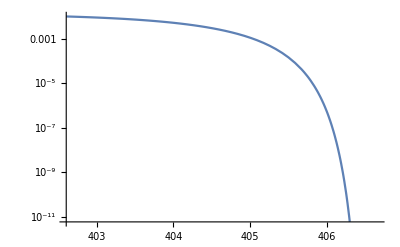

0

```mathematica
(* limit of energy domain *)
maxϵ=μ+σ/3;
μ=400;
σ=20;
LogPlot[dNdϵ[x,μ,σ],{x,0.99maxϵ,maxϵ}]
Clear[μ,σ]

Limit[dNdϵ[x,μ,σ],x->∞]
```

```mathematica
(* this distribution has ≠ 0 value at origin *)
dNdϵ[0,μ,σ]
```

ⅇ^(-σ/(2 (μ+σ/3)))/(μ+σ/3)^(3/2)

Appendix A

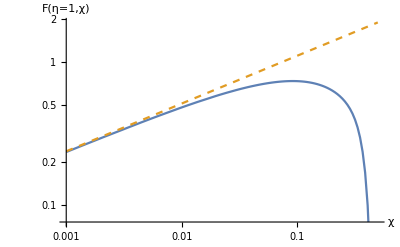

```mathematica
Clear[F,Fapprox,η,χ]
F[η_,χ_]:=(4χ)/(3η^2)((1-(2χ)/η+1/(1-2χ/η))BesselK[2/3,(4χ)/(3η^2(1-2χ/η))]-NIntegrate[BesselK[1/3,t],{t,(4χ)/(3η^2(1-2χ/η)),∞}])
Fapprox[η_,χ_]:=(16/3)^(1/3) Gamma[2/3] η^(-2/3) χ^(1/3)
η=1;
LogLogPlot[{F[η,χ],Fapprox[η,χ]},{χ,0.001η,η/2},PlotPoints->3,AxesLabel->{"χ","F(η=1,χ)"},PlotStyle->{Default,Dashed}]
Clear[η]
```

Low χ expansion

```mathematica
Clear[η,χ]
Refine[Series[(4χ)/(3η^2)((1-(2χ)/η+1/(1-2χ/η))BesselK[2/3,(4χ)/(3η^2(1-2χ/η))]-Integrate[BesselK[1/3,t],{t,(4χ)/(3η^2(1-2χ/η)),∞}]),{χ,0,1}]//Normal,{χ>0,η>0}]//FullSimplify
```

Piecewise[{{-(4 π χ)/(3 √3 η^2)+(2 (2/3)^(1/3) χ^(1/3) Gamma[2/3])/η^(2/3), η (η-2 χ) χ>0&&η≥2 χ}, {-(4 (-1)^(2/3) π (-η)^(2/3) χ)/(3 √3 η^(8/3))+(2 (2/3)^(1/3) χ^(1/3) Gamma[2/3])/η^(2/3), True}}]

Figure B1

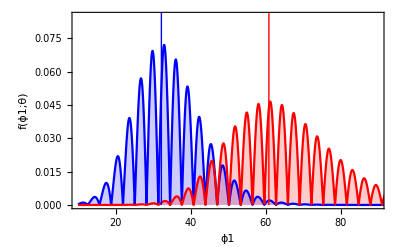

```mathematica
W[x_]:=ProductLog[0,x](* Lambert Function *)

w0=2; (* [μm] *)
λ = 0.8; (* [μm] *)
k=2π/λ; (* [1/μm] *)
ω = 2π/λ; (* [1/μm] *)
f = 9; (* [μm] *)
Int = 10^22; (* W/cm^2*)
(* Compton time *)
τC =10^-6.5;(* ℏ/(m c^2)*) (* ??? *)
ESch = 1.3*10^16; (* [V/cm] *)
E0 = Sqrt[(2 Int)/(c ϵ0)]//N;(* [V/cm]*)

ζ[θ_]:=Sqrt[Sin[θ]^2/((1+Cos[θ])^2 k^2 w0^2)+(2Log[2])/(k^2 f^2)](*(B.6)*)
dτdϕ[ϕ_,θ_]:=-(5α)/(2√3 ω τC)E0/ESch Abs[Sin[ϕ]] Exp[-ζ[θ]^2 ϕ^2] (*(B.5)*) (**)
τf[ϕ1_,θ_]:=(5 α)/(2√(3π) ω τC)E0/ESch(1-Erf[ζ[θ] ϕ1])/ζ[θ](*(B.7)*)
fϕ1[ϕ1_,θ_]:=Exp[-τf[ϕ1,θ]]Abs[dτdϕ[ϕ1,θ]](*(B.8)*)
ϕ1mp[θ_]:=Sqrt[1/(2ζ[θ]^2)W[1/ζ[θ]^2((5α)/(√6 π)1/(ω τC)E0/ESch)^2]](* (B.9) *)

plt=Plot[{fϕ1[ϕ1 ,π/3],fϕ1[ϕ1 ,π/6]},{ϕ1,10,100},PlotRange->{{10,90},{0,0.085}},Axes->False,Frame->True,PlotStyle->{Blue,Red},Filling->0,FrameLabel->{"ϕ1","f(ϕ1;θ)"}];
line1=Graphics[{Blue,Line[{{ϕ1mp[π/3],0},{ϕ1mp[π/3],0.09}}]}];
line2=Graphics[{Red,Line[{{ϕ1mp[π/6],0},{ϕ1mp[π/6],0.09}}]}];
Show[{plt,line1,line2}]
```